DEVBIO 232 Homework 2

February 15th, 2019
Samuel Morabito

#### Problem 1: Model negative, positive, and no autoregulation

## -Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
noAutoreg = {
Y'[t] == p -r Y[t], Y[0] == Yzero
};

posAutoreg = {
Y'[t] == p (Y[t]/(k + Y[t])) -r Y[t], Y[0] == Yzero
};
negAutoreg = {
Y'[t] == p (k/(k + Y[t])) -r Y[t], Y[0] == Yzero
};

(* define parameters for these ODEs*)
noParams = {p-> 1, Yzero-> 0, r-> 1};
negParams = {p-> 1, Yzero -> 0, r-> 0.5, k->1};
posParams = {p->4, Yzero-> 0.01, r->2, k->1};

(* replace symbols with parameter values for each ODE *)
noCase = noAutoreg /. noParams;
negCase = negAutoreg /. negParams;
posCase = posAutoreg /. posParams;

(* use NDSolve to get the numerical solution to these ODEs *)
solNoAutoreg = NDSolve[noCase, Y[t], {t, 0, 10}];
solNegAutoreg = NDSolve[negCase, Y[t], {t, 0, 10}];
solPosAutoreg = NDSolve[posCase, Y[t], {t, 0, 10}];
```

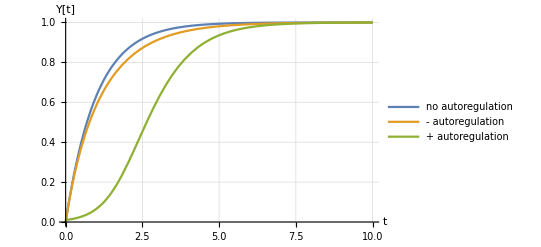

```mathematica
(* plot the solutions *)
Plot[{Y[t] /. solNoAutoreg, Y[t]/.solNegAutoreg, Y[t]/.solPosAutoreg}, {t, 0, 10}, AxesLabel-> {"t", "Y[t]"}, GridLines-> Automatic, PlotLegends-> {"no autoregulation", "- autoregulation", "+ autoregulation"}]
```

#### Problem 2: Cascades

2a: Model one or the other of these below cascades:

```mathematica
ClearAll["Global`*"]
```

```mathematica
xPrime = Piecewise[{{Y[t]/.solPosAutoreg, t > 0}, {0, t<0}}];
yPrime = Piecewise[{{Y[t]/.solPosAutoreg, t > thresh}, {0, t<thresh}}]; (*need to find thresh time based on when the previous function is at the thresh value*)
```

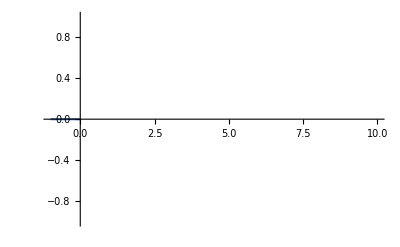

```mathematica
Plot[xPrime, {t, -1, 10}]
```